```mathematica
Quit[]
```

```mathematica
ClearAll["Global`*"];
W=Function[s,Exp[-s^2/(.16)^2]];
```

The Eulerian formulation picks up extra terms when taking time derivatives via the following relation:
If f(s,t) = F(S0(s,t),t), then f_t=F_t+F_S0(∂S0)/(∂t), and (∂f)/(∂s)=(∂F)/(∂S0)(∂S0)/(∂s)=αγ(∂F)/(∂S0)
Space derivatives translate in a more obvious way: ∂/(∂S0)=∂/(∂s)(∂s)/(∂S0)=αγ∂/(∂s)

## Set-up: pre-homeostasis mechanochemical growth

```mathematica
W=Function[s,Exp[-s^2/(.16)^2]];
Subs ={μ->10,ρ->10,ns->-.5,k->1000};
```

```mathematica
(* Lagrangian formulation *)
SolPreHomeostasisLagrangian=NDSolve[{D[s[S0, t],S0]==(1+n[S0, t])γ[S0,t],
D[γ[S0,t],t]==γ[S0,t](W[s[S0, t]]+μ*(n[S0, t]-ns)*1/2*(1+Tanh[50*(ns-n[S0, t])])),
D[n[S0, t], S0]==k*(1+n[S0, t])γ[S0,t]*(s[S0, t]-p[S0, t]),
D[p[S0, t], t]==ρ*(s[S0, t]-p[S0, t]),
s[0,t]==0,s[1,t]==1,γ[S0,0]==1,s[S0,0]==S0, p[S0, 0]==S0, n[S0, 0]==0}/.Subs,{s,γ, n, p},{S0,0,1},{t,0,6},MaxStepSize-> 0.005,Method->{"IndexReduction"->Automatic}][[1]];
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

```mathematica
sS0 = Function[S0,  Evaluate[s[S0, t]/.SolPreHomeostasisLagrangian/.t-> 1]];
gammaS0 = Function[S0,  Evaluate[γ[S0, t]/.SolPreHomeostasisLagrangian/.t-> 1]];
nS0=Function[S0, Evaluate[n[S0, t]/.SolPreHomeostasisLagrangian/.t-> 1]];
pS0=Function[S0, Evaluate[p[S0, t]/.SolPreHomeostasisLagrangian/.t-> 1]];
gS0 =Function[S0, (Evaluate[D[γ[S0, t]/.SolPreHomeostasisLagrangian,t]]/.t-> 1)/Evaluate[γ[S0, t]/.SolPreHomeostasisLagrangian/.t-> 1]];
```

```mathematica
Manipulate[Plot[Evaluate[D[γ[S0, t]/.SolPreHomeostasisLagrangian, t]/.t-> T]/(γ[S0, t]/.SolPreHomeostasisLagrangian/.t-> T),{S0, 0, 1},PlotRange-> {{0, 1}, {0, 1}}], {T, 0, 6}]
```

```mathematica
(* Eulerian formulation *)
SolPreHomeostasisEulerian=NDSolve[{D[S0[s, t],s]==1/((1+n[s, t])γ[s,t]),
D[γ[s,t],t]==γ[s,t](W[s]+μ*(n[s, t]-ns)*1/2*(1+Tanh[50*(ns-n[s, t])]))+(1+n[s,t])*γ[s,t]*D[γ[s,t], s]*D[S0[s, t], t],
D[n[s, t], s]==k*(s-p[s, t]),
D[p[s, t], t]==ρ*(s-p[s, t])+(1+n[s,t])*γ[s,t]*D[p[s,t], s]*D[S0[s, t], t],
S0[0,t]==0,S0[1,t]==1,γ[s,0]==1,S0[s,0]==s, p[s, 0]==s, n[s, 0]==0}/.Subs,{S0,γ, n, p},{s,0,1},{t,0,6},MaxStepSize-> 0.005,Method->{"IndexReduction"->Automatic}][[1]];
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

```mathematica
(* Define the initial growth, stress, and S0 as per the T = 1 case, so that we are only changing g(s) *)
αs = Function[s, 1+n[s, t]/.SolPreHomeostasisEulerian/.t-> 1];
gammas=Function[s,γ[s, t]/.SolPreHomeostasisEulerian/.t-> 1];S0s=Function[s,  S0[s, t]/.SolPreHomeostasisEulerian/.t-> 1];
gs =Function[s, (Evaluate[D[γ[s, t]/.SolPreHomeostasisEulerian,t]]/.t-> 1)/ Evaluate[γ[s, t]/.SolPreHomeostasisEulerian/.t-> 1]];
ps=Function[s, p[s,t]/.SolPreHomeostasisEulerian/.t-> 1];
```

```mathematica
vs=Function[s,Evaluate[(-ρ*D[αs[s]-1,s]/(k*D[ps[s],s]))/.Subs]];
```

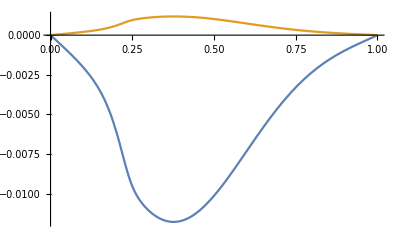

```mathematica
Plot[{vs[s],(s-ps[s])},{s, 0, 1}]
```

```mathematica
Clear[ns]
```

```mathematica
AgeSolPreHomeostasisEulerian=NDSolve[{D[A[s, t], t]==1-(Evaluate[D[γ[s, t]/.SolPreHomeostasisEulerian,t]])/Evaluate[γ[s, t]/.SolPreHomeostasisEulerian]*A[s,t]+((1+n[s,t])*γ[s,t]*D[A[s,t], s]*D[S0[s, t], t]/.SolPreHomeostasisEulerian), A[s, 0]==0}/.Subs,A,{s,0,1},{t,0,6},MaxStepSize-> 0.005,Method->{"IndexReduction"->Automatic}][[1]];
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

```mathematica
As=Function[s, A[s,t]/.AgeSolPreHomeostasisEulerian/.t-> 1];
```

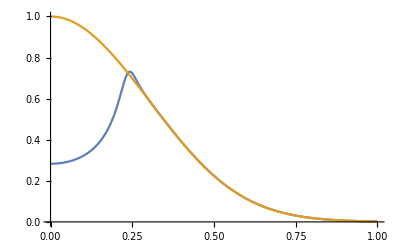

```mathematica
Plot[{gs[s], gswnt[s]},{s, 0, 1}]
```

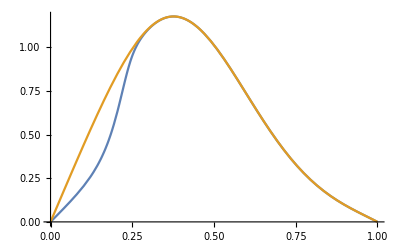

```mathematica
Plot[{-100*vs[s],-100*vswnt[s]},{s, 0, 1}]
```

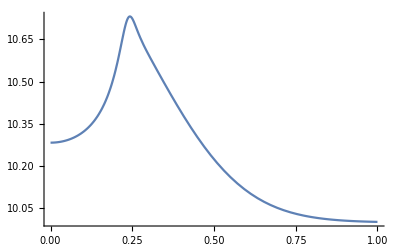

```mathematica
Plot[gs[s]+ρ/.Subs,{s, 0, 1}]
```

```mathematica
(* Compare with Wnt formulation *)
(* Eulerian formulation *)
SolPreHomeostasisWntEulerian=NDSolve[{D[S0[s, t],s]==1/((1+n[s, t])γ[s,t]),
D[γ[s,t],t]==γ[s,t](W[s])+(1+n[s,t])*γ[s,t]*D[γ[s,t], s]*D[S0[s, t], t],
D[n[s, t], s]==k*(s-p[s, t]),
D[p[s, t], t]==ρ*(s-p[s, t])+(1+n[s,t])*γ[s,t]*D[p[s,t], s]*D[S0[s, t], t],
S0[0,t]==0,S0[1,t]==1,γ[s,0]==1,S0[s,0]==s, p[s, 0]==s, n[s, 0]==0}/.Subs,{S0,γ, n, p},{s,0,1},{t,0,6},MaxStepSize-> 0.005,Method->{"IndexReduction"->Automatic}][[1]];
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

```mathematica
AgeSolPreHomeostasisWntEulerian=NDSolve[{D[A[s, t], t]==1-(Evaluate[D[γ[s, t]/.SolPreHomeostasisWntEulerian,t]])/Evaluate[γ[s, t]/.SolPreHomeostasisWntEulerian]*A[s,t]+((1+n[s,t])*γ[s,t]*D[A[s,t], s]*D[S0[s, t], t]/.SolPreHomeostasisWntEulerian), A[s, 0]==0}/.Subs,A,{s,0,1},{t,0,6},MaxStepSize-> 0.005,Method->{"IndexReduction"->Automatic}][[1]];
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

```mathematica
Manipulate[Plot[{A[s, t]/.AgeSolPreHomeostasisEulerian,A[s,t]/.AgeSolPreHomeostasisWntEulerian},{s, 0, 1},PlotRange-> {0, 5}],{t, 0, 5}]
```

ReplaceAll::reps: {AgeSolPreHomeostasisEulerian} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {AgeSolPreHomeostasisEulerian} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {AgeSolPreHomeostasisWntEulerian} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {AgeSolPreHomeostasisEulerian} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {AgeSolPreHomeostasisEulerian} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {AgeSolPreHomeostasisEulerian} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

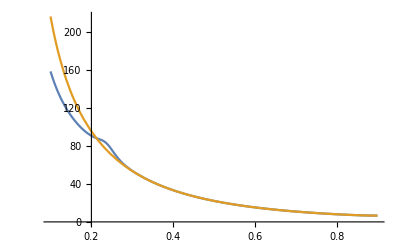

```mathematica
Plot[{-gs[s]/vs[s],-gswnt[s]/vswnt[s]},{s, 0.1, 0.9}]
```

```mathematica
(* Define the initial growth, stress, and S0 as per the T = 1 case, so that we are only changing g(s) *)
nswnt=Function[s, n[s, t]/.SolPreHomeostasisWntEulerian/.t-> 1];
αswnt = Function[s, 1+n[s, t]/.SolPreHomeostasisWntEulerian/.t-> 1];
gammaswnt=Function[s,γ[s, t]/.SolPreHomeostasisWntEulerian/.t-> 1];S0swnt=Function[s,  S0[s, t]/.SolPreHomeostasisWntEulerian/.t-> 1];
gswnt =Function[s, (Evaluate[D[γ[s, t]/.SolPreHomeostasisWntEulerian,t]]/.t-> 1)/ Evaluate[γ[s, t]/.SolPreHomeostasisWntEulerian/.t-> 1]];
pswnt=Function[s, p[s,t]/.SolPreHomeostasisWntEulerian/.t-> 1];
```

```mathematica
vswnt=Function[s,Evaluate[(-ρ*D[αswnt[s]-1,s]/(k*D[pswnt[s],s]))/.Subs]];
```

## Base case: Homeostasis (g(s) taken at t = 1)

```mathematica
SolHomeostasisEulerianControl=NDSolve[{D[γ[s,t],t]==γ[s,t]*gs[s]+vs[s]*D[γ[s,t],s],
γ[s,0]==gammas[s]}/.Subs,{γ},{s,0,1},{t,0, 10},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

```mathematica
S0SolHomeostasisEulerianControl=NDSolve[{D[S0[s,t],s]==1/(αs[s]*γ[s,t]/.SolHomeostasisEulerianControl),
S0[0,t]==0}/.Subs,{S0},{s,0,1},{t,0, 10},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];
```

```mathematica
LmuControl = Function[t, S0[s,t]/.S0SolHomeostasisEulerianControl/.s-> 1];
```

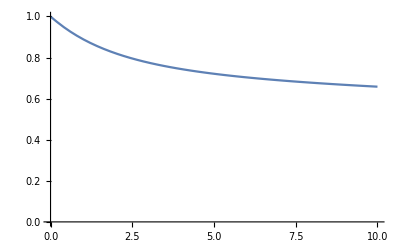

```mathematica
Plot[LmuControl[t],{t, 0, 10},PlotRange-> {0, 1}]
```

```mathematica
FullSolHomeostasisEulerian=NDSolve[{D[S0[s, t],s]==1/((1+n[s, t])γ[s,t]),
D[γ[s,t],t]==γ[s,t](W[s]+μ*(n[s,t]-ns)*1/2*(1+Tanh[50*(ns-n[s,t])]))+(1+n[s,t])*γ[s,t]*D[γ[s,t], s]*D[S0[s, t], t],
D[n[s, t], s]==k/((1+n[s,t])*γ[s,t])*(s-p[s, t]),
D[p[s, t], t]==ρ*(s-p[s, t])+(1+n[s,t])*γ[s,t]*D[p[s,t], s]*D[S0[s, t], t],
S0[0,t]==0,S0[1, t]==LmuControl[t],S0[s,0]==S0s[s],γ[s,0]==gammas[s], p[s, 0]==ps[s], n[s, 0]==αs[s]-1}/.Subs,{S0,γ, n, p},{s,0,1},{t,0,10},MaxStepSize-> 0.005,Method->{"IndexReduction"->Automatic}][[1]];
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

InterpolatingFunction::dmval: Input value {1, -0.0001} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
γ[s,t]/.SolHomeostasisEulerianControl/.t->5
```

InterpolatingFunction[{{0., 1.}, {0., 10.}}, <>][s,5]

```mathematica
n[s,t]/.FullSolHomeostasisEulerian/.s-> 0/.t-> 0
```

-0.548725

```mathematica
Manipulate[Plot[n[s,t]/.FullSolHomeostasisEulerian,{s, 0, 1},PlotRange->Full],{t, 0, 10}]
```

ReplaceAll::reps: {FullSolHomeostasisEulerian} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
Manipulate[Plot[γ[s,t]/.FullSolHomeostasisEulerian,{s, 0, 1},PlotRange->Full],{t, 0, 10}]
```

ReplaceAll::reps: {FullSolHomeostasisEulerian} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
AgeSolHomeostasisEulerianControl=NDSolve[{D[A[s,t],t]==1-gs[s]*A[s,t]+vs[s]*D[A[s,t],s],
A[s,0]==As[s]}/.Subs,{A},{s,0,1},{t,0, 5},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

```mathematica
Manipulate[Plot[γ[s,t]/.SolHomeostasisEulerianControl,{s, 0, 1}],{t, 0, 5}]
```

ReplaceAll::reps: {SolHomeostasisEulerianControl} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {SolHomeostasisEulerianControl} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {SolHomeostasisEulerianControl} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

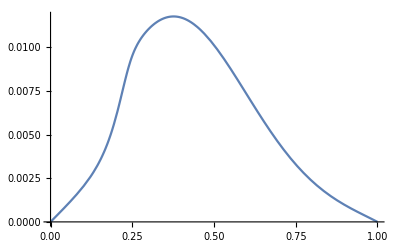

```mathematica
Plot[-vs[s],{s, 0, 1}]
```

```mathematica
D[αs[s],s]
```

InterpolatingFunction[{{0., 1.}, {0., 6.}}, <>][s,1]

```mathematica
sValues = Range[0, 1, 0.005];
```

```mathematica
gsMax = Max[gs[sValues]]
```

0.730196

```mathematica
vsol=NDSolve[{v'[s]-(v[s]*αs'[s])/αs[s]==-gs[s],v[0]==0},v,{s, 0, 1}][[1]];
```

```mathematica
ns/.Subs
```

```mathematica
Series[1/2*(1+Tanh[50*(n0-n)]),{n, n0, 2}]
```

1/2-25 (n-n0)+O[n-n0]^3

```mathematica
vhom=Function[s,v[s]/.vsol];
```

```mathematica
HomeostasisEulerianSolWithVHom = NDSolve[{D[S0[s,t],s]==1/(αs[s]*γ[s,t]),D[γ[s,t],t]==γ[s,t]*gs[s]+vhom[s]*D[γ[s,t],s],
S0[0,t]==0,S0[s, 0]==S0s[s], γ[s,0]==gammas[s]}/.Subs,{S0,γ},{s,0,1},{t,0, 5},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

```mathematica
LmuWithVHom=Function[t, S0[s,t]/.HomeostasisEulerianSolWithVHom/.s-> 1];
```

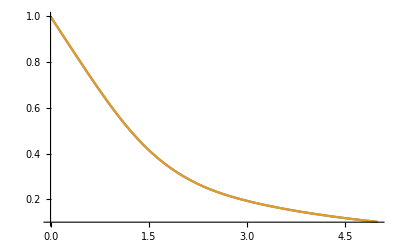

```mathematica
Plot[{LmuWithVHom[t],LmuControl[t]}, {t, 0, 5}]
```

```mathematica
vs[s]
```

Function[s,v[s]/.vsol]

```mathematica
Manipulate[Plot[{αs[s]*γ[s,t]*D[S0[s,t],t]/.SolHomeostasisEulerian/.s-> S/.t-> T,vhom[S],vs[S]},{S, 0, 1}],{T, 0, 5}]
```

ReplaceAll::reps: {SolHomeostasisEulerian} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {SolHomeostasisEulerian} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {SolHomeostasisEulerian} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

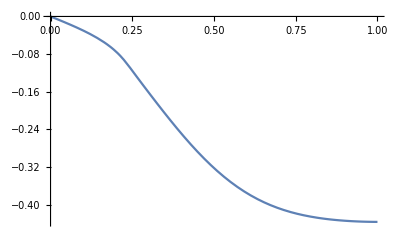

```mathematica
Plot[vhom[s],{s, 0, 1}]
```

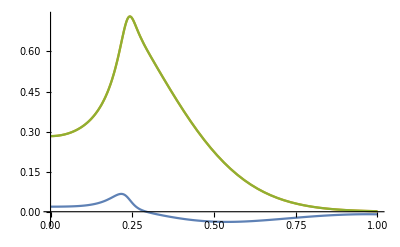

```mathematica
Plot[{-(D[vs[s],s]-D[αs[s],s]/αs[s]*vs[s])/.s-> S,-(D[v[s]/.vsol,s]-D[αs[s],s]/αs[s]*v[s]/.vsol)/.s-> S,gs[S]},{S, 0, 1}]
```

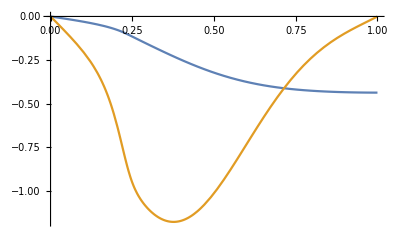

```mathematica
Plot[{v[s]/.vsol,100*vs[s]},{s, 0, 1}]
```

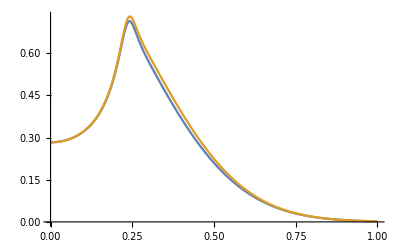

```mathematica
Plot[{W[s]+μ*(αs[s]-1-ns)*1/2*(1+Tanh[50*(ns-αs[s]+1)])/.Subs,gs[s]},{s, 0, 1}]
```

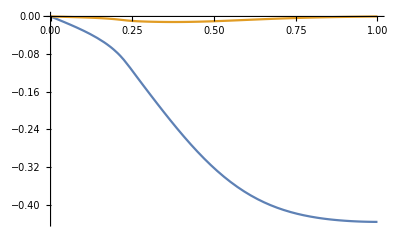

```mathematica
Plot[{v[s]/.vsol,vs[s]},{s, 0, 1}]
```

```mathematica
vhom=Function[s, v[s]/.vsol];
```

```mathematica
SolHomeostasisEulerian=NDSolve[{D[S0[s, t],s]==1/(αs[s]*γ[s,t]),
D[γ[s,t],t]==γ[s,t]*gs[s]+αs[s]*γ[s,t]*D[S0[s,t],t]*D[γ[s,t],s],
S0[s, 0]==S0s[s], S0[0,t]==0,γ[s,0]==gammas[s]}/.Subs,{S0,γ},{s,0,1},{t,0, 5},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

```mathematica
AgeSolHomeostasisEulerian=NDSolve[{D[A[s,t],t]==1-gs[s]*A[s,t]+vhom[s]*D[A[s,t],s],
A[s,0]==As[s]}/.Subs,{A},{s,0,1},{t,0, 5},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

```mathematica
Manipulate[Plot[A[s,t]/.AgeSolHomeostasisEulerian,{s, 0, 1}],{t, 0, 5}]
```

ReplaceAll::reps: {AgeSolHomeostasisEulerian} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {AgeSolHomeostasisEulerian} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {AgeSolHomeostasisEulerian} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {AgeSolHomeostasisEulerian} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
LmuControl= Function[t, S0[s, t]/.SolHomeostasisEulerian/.s-> 1];
```

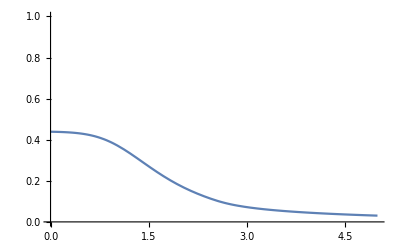

```mathematica
Plot[-D[LmuControl[t],t]/.t-> T,{T, 0, 5},PlotRange-> {0, 1}]
```

```mathematica
ns/.Subs
```

-0.5

```mathematica
FullSolHomeostasisEulerian=NDSolve[{D[S0[s, t],s]==1/((1+n[s, t])γ[s,t]),
D[γ[s,t],t]==γ[s,t](W[s]+μ*(n[s,t]-ns)*1/2*(1+Tanh[50*(ns-n[s,t])]))+(1+n[s,t])*γ[s,t]*D[γ[s,t], s]*D[S0[s, t], t],
D[n[s, t], s]==k/((1+n[s,t])*γ[s,t])*(s-p[s, t]),
D[p[s, t], t]==ρ*(s-p[s, t])+(1+n[s,t])*γ[s,t]*D[p[s,t], s]*D[S0[s, t], t],
S0[0,t]==0,S0[1, t]==LmuControl[t],S0[s,0]==S0s[s],γ[s,0]==gammas[s], p[s, 0]==ps[s], n[s, 0]==αs[s]-1}/.Subs,{S0,γ, n, p},{s,0,1},{t,0,5},MaxStepSize-> 0.005,Method->{"IndexReduction"->Automatic}][[1]];
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

InterpolatingFunction::dmval: Input value {1, -0.0001} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Manipulate[Plot[{γ[s,t]/.FullSolHomeostasisEulerian},{s, 0, 1},PlotRange-> Full],{t, 0, 5}]
```

ReplaceAll::reps: {FullSolHomeostasisEulerian} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
Manipulate[Plot[{n[s,t]/.FullSolHomeostasisEulerian,αs[s]-1},{s, 0, 1},PlotRange-> {-1, 0}],{t, 0, 5}]
```

ReplaceAll::reps: {FullSolHomeostasisEulerian} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

## Effect of incremental gamma profiles on sloughing boundaries

First examine the effect of scale on sloughing.

```mathematica
gValues = {0.25, 0.5, 1, 2, 4};
IncGammaPlotSetsScale = {};
IncGammaSetsScale = {};
NetIncGammaSetsScale = {};
LMuPlotSetsScale = {};
LMuSetsScale = {};
LMuDataScale = {};
IncGammaDataScale={};
```

```mathematica
index = 1;
While[(index ≤Length[gValues]),  
g = gValues[[index]];
Clear[Gs];
(* Define functions needed for homeostasis *)
Gs=Function[s, g*gs[s]];

SolHomeostasisEulerian=NDSolve[{D[S0[s, t],s]==1/(αs[s]*γ[s,t]),
D[γ[s,t],t]==γ[s,t]*Gs[s]+αs[s]γ[s,t]D[γ[s,t],s]D[S0[s,t],t],
S0[s, 0]==S0s[s], S0[0,t]==0,γ[s,0]==gammas[s]}/.Subs,{S0,γ},{s,0,1},{t,0, 5},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];

(* Calculate Lmu as a function of time *)
Lmu=Function[t, S0[s, t]/.SolHomeostasisEulerian/.s-> 1];

P1=Plot[Gs[s],{s, 0, 1},PlotStyle->ColorData[97,index+1],PlotPoints-> 50];
P2=Plot[Lmu[t],{t, 0, 5},PlotStyle->ColorData[97,index+1],PlotRange-> {{0, 5}, {0, 1}}, PlotPoints-> 100];
AppendTo[IncGammaPlotSetsScale,P1];
AppendTo[LMuPlotSetsScale,P2];

AppendTo[IncGammaSetsScale, Gs];
AppendTo[LMuSetsScale, Lmu];

AppendTo[NetIncGammaSetsScale, NIntegrate[Gs[s], {s, 0, 1}]];
AppendTo[LMuDataScale, Lmu[N[Range[0, 2500, 5]]/500]];
AppendTo[IncGammaDataScale,Gs[N[Range[0, 500, 5]]/500]];
index=index+1];
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

General::stop: Further output of NDSolve :: ntdvdae will be suppressed during this calculation.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

General::stop: Further output of NDSolve :: bcart will be suppressed during this calculation.

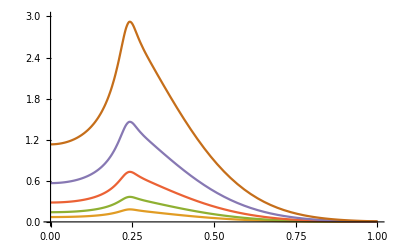

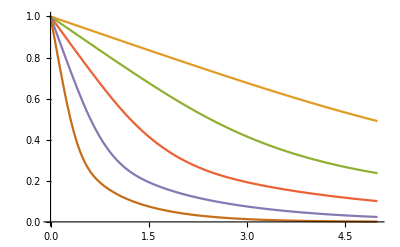

```mathematica
Show[IncGammaPlotSetsScale, PlotRange-> {{0, 1}, {0, 3}}]
Show[LMuPlotSetsScale,PlotRange-> {{0, 5}, {0, 1}}]
```

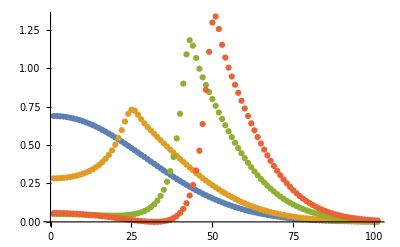

```mathematica
ListPlot[Table[IncGammaDataShape[[i]],{i, 1, 4}]]
```

```mathematica
(* Save the data *)
```

```mathematica
sValues=N[Range[0, 500, 5]]/500;
tValues=N[Range[0, 2500, 5]]/500;
```

```mathematica
index = 1;
While[(index ≤Length[gValues]),
Export[StringJoin["~/Documents/MorphoCrypt/Mathematica/homeostaticincgrowth_g_",ToString[gValues[[index]]],".csv"] ,Table[{sValues[[i]], IncGammaDataScale[[index]][[i]]},{i, 1, Length[sValues]}]]; 
Export[StringJoin["~/Documents/MorphoCrypt/Mathematica/sloughingboundary_g_",ToString[gValues[[index]]],".csv"] ,Table[{tValues[[i]], LMuDataScale[[index]][[i]]},{i, 1, Length[tValues]}]];
index=index+1];
```

```mathematica
gsScale=NIntegrate[gs[s],{s, 0, 1}]
```

0.244066

Now let’s test the effect of shape on sloughing.

```mathematica
TValues = {0,1, 2, 3, 4,5};
IncGammaPlotSetsShape = {};
IncGammaSetsShape = {};
NetIncGammaSetsShape ={};
LMuPlotSetsShape = {};
LMuSetsShape = {};
LMuDataShape= {};
IncGammaDataShape={};
```

```mathematica
index = 1;
While[(index ≤Length[TValues]),  
T = TValues[[index]];
Clear[Gs];
(* Define functions needed for homeostasis *)
Gs=Function[s, (Evaluate[D[γ[s, t]/.SolPreHomeostasisEulerian,t]]/.t-> T)/Evaluate[γ[s, t]/.SolPreHomeostasisEulerian/.t-> T]];
GsScale=NIntegrate[Gs[s], {s, 0, 1}];
GsScaled=Function[s,Evaluate[ (Gs[s] gsScale)/GsScale]];

SolHomeostasisEulerian=NDSolve[{D[S0[s, t],s]==1/(αs[s]*γ[s,t]),
D[γ[s,t],t]==γ[s,t]*(Gs[s]*gsScale)/GsScale+αs[s]γ[s,t]D[γ[s,t],s]D[S0[s,t],t],
S0[s, 0]==S0s[s], S0[0,t]==0,γ[s,0]==gammas[s]}/.Subs,{S0,γ},{s,0,1},{t,0, 5},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];

(* Calculate Lmu as a function of time *)
Lmu=Function[t, S0[s, t]/.SolHomeostasisEulerian/.s-> 1];

P1=Plot[GsScaled[s],{s, 0, 1},PlotStyle->ColorData[97,index+1],PlotPoints-> 50];
P2=Plot[Lmu[t],{t, 0, 5},PlotStyle->ColorData[97,index+1],PlotRange-> {{0, 5}, {0, 1}}, PlotPoints-> 100];
AppendTo[IncGammaPlotSetsShape,P1];
AppendTo[LMuPlotSetsShape,P2];

AppendTo[IncGammaSetsShape,GsScaled];
AppendTo[LMuSetsShape, Lmu];

AppendTo[NetIncGammaSetsShape, NIntegrate[Gs[s], {s, 0, 1}]];
AppendTo[LMuDataShape, Lmu[N[Range[0, 2500, 5]]/500]];
sValues = N[Range[0, 500, 5]]/500;
AppendTo[IncGammaDataShape, Table[GsScaled[sValues[[i]]],{i, 1, Length[sValues]}]];
index=index+1];
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

General::stop: Further output of NDSolve :: ntdvdae will be suppressed during this calculation.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

General::stop: Further output of NDSolve :: bcart will be suppressed during this calculation.

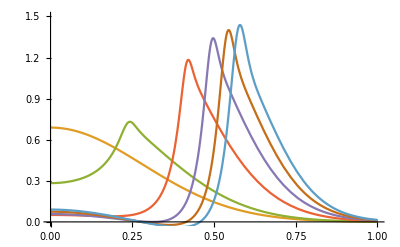

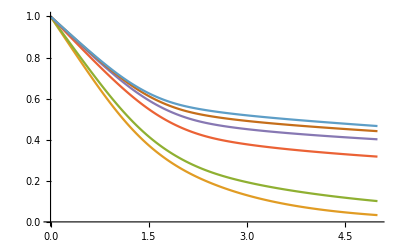

```mathematica
Show[IncGammaPlotSetsShape, PlotRange-> {{0, 1}, {0, 1.5}}]
Show[LMuPlotSetsShape,PlotRange-> {{0, 5}, {0, 1}}]
```

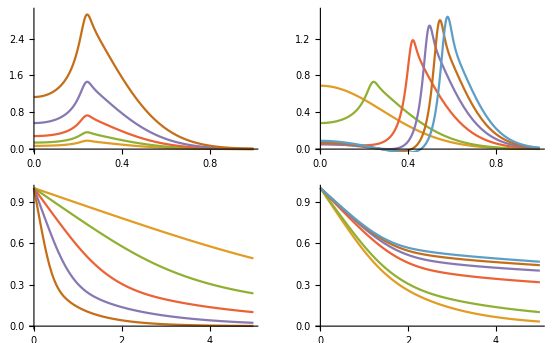

```mathematica
GraphicsGrid[{{Show[IncGammaPlotSetsScale,PlotRange-> {{0, 1}, {0, 3}}],Show[IncGammaPlotSetsShape,PlotRange-> {{0, 1}, {0, 1.5}}]},{Show[LMuPlotSetsScale,PlotRange-> {{0, 5}, {0, 1}}],Show[LMuPlotSetsShape,PlotRange-> {{0, 5}, {0, 1}}]}}]
```

```mathematica
sS0 = Function[S0,  Evaluate[s[S0, t]/.SolPreHomeostasisLagrangian/.t-> T]];
gammaS0 = Function[S0,  Evaluate[γ[S0, t]/.SolPreHomeostasisLagrangian/.t-> T]];
```

```mathematica
index = 1;
While[(index ≤Length[TValues]),
Export[StringJoin["~/Documents/MorphoCrypt/Mathematica/homeostaticincgrowth_T_",ToString[TValues[[index]]],".csv"] ,Table[{sValues[[i]], IncGammaDataShape[[index]][[i]]},{i, 1, Length[sValues]}]]; 
Export[StringJoin["~/Documents/MorphoCrypt/Mathematica/sloughingboundary_T_",ToString[TValues[[index]]],".csv"] ,Table[{tValues[[i]], LMuDataShape[[index]][[i]]},{i, 1, Length[tValues]}]];
index=index+1];
```

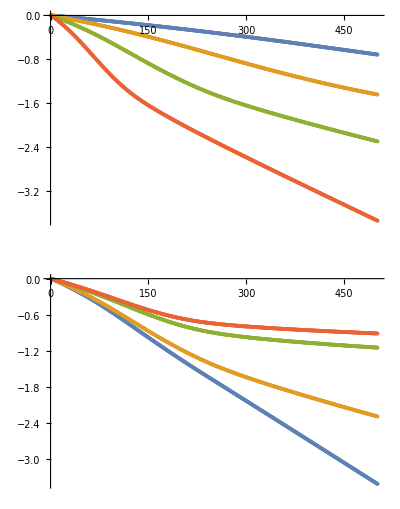

```mathematica
GraphicsGrid[{{ListPlot[Table[Log[LMuDataScale[[i]]],{i, 1, 4}]]}, {ListPlot[Table[Log[LMuDataShape[[i]]],{i, 1, 4}]]}}]
```

## Connecting ageing to sloughing

Let’s work out the sloughing rates as well

```mathematica
gValues = {0.25, 0.5, 1, 2, 4};
MuDataScale = {};
MuDotDataScale={};
```

```mathematica
index = 1;
While[(index ≤Length[gValues]),  
g = gValues[[index]];
Clear[Gs];
(* Define functions needed for homeostasis *)
Gs=Function[s, g*gs[s]];

SolHomeostasisEulerian=NDSolve[{D[S0[s, t],s]==1/(αs[s]*γ[s,t]),
D[γ[s,t],t]==γ[s,t]*Gs[s]+αs[s]γ[s,t]D[γ[s,t],s]D[S0[s,t],t],
S0[s, 0]==S0s[s], S0[0,t]==0,γ[s,0]==gammas[s]}/.Subs,{S0,γ},{s,0,1},{t,0, 5},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];

(* Calculate Lmu as a function of time *)
Lmu=Function[t, S0[s, t]/.SolHomeostasisEulerian/.s-> 1];
Mu = Function[t, 1-Lmu[t]];
MuDot=Function[t, Evaluate[D[Mu[t],t]]];

AppendTo[MuDataScale,Mu[N[Range[0, 2500, 5]]/500]];
AppendTo[MuDotDataScale,MuDot[N[Range[0, 2500, 5]]/500]];
index=index+1];
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

General::stop: Further output of NDSolve :: ntdvdae will be suppressed during this calculation.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

General::stop: Further output of NDSolve :: bcart will be suppressed during this calculation.

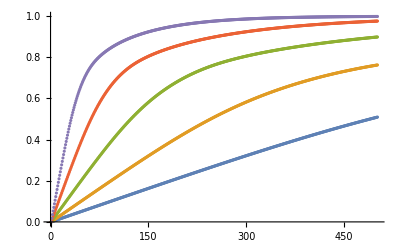

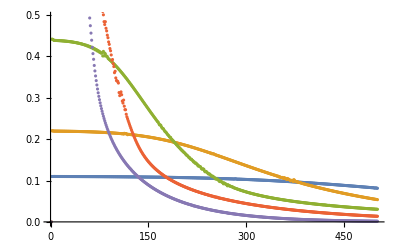

```mathematica
ListPlot[Table[MuDataScale[[i]],{i, 1, Length[gValues]}]]
ListPlot[Table[MuDotDataScale[[i]],{i, 1, Length[gValues]}]]
```

```mathematica
tValues=N[Range[0, 2500, 5]]/500;
```

```mathematica
index = 1;
While[(index ≤Length[gValues]),
Export[StringJoin["~/Documents/MorphoCrypt/Mathematica/Solutions/amountsloughedscale_g_",ToString[gValues[[index]]],".csv"] ,Table[{tValues[[i]], MuDataScale[[index]][[i]]},{i, 1, Length[tValues]}]]; 
Export[StringJoin["~/Documents/MorphoCrypt/Mathematica/Solutions/sloughingratescale_g_",ToString[gValues[[index]]],".csv"] ,Table[{tValues[[i]], MuDotDataScale[[index]][[i]]},{i, 1, Length[tValues]}]];
index=index+1];
```

```mathematica
gsScale=NIntegrate[gs[s],{s,0,1}]
```

0.244066

```mathematica
TValues = {0,1, 2, 3, 4,5};
MuDataShape= {};
MuDotDataShape={};
```

```mathematica
index = 1;
While[(index ≤Length[TValues]),  
T = TValues[[index]];
Clear[Gs];
(* Define functions needed for homeostasis *)
Gs=Function[s, (Evaluate[D[γ[s, t]/.SolPreHomeostasisEulerian,t]]/.t-> T)/Evaluate[γ[s, t]/.SolPreHomeostasisEulerian/.t-> T]];
GsScale=NIntegrate[Gs[s], {s, 0, 1}];
GsScaled=Function[s,Evaluate[ (Gs[s] gsScale)/GsScale]];

SolHomeostasisEulerian=NDSolve[{D[S0[s, t],s]==1/(αs[s]*γ[s,t]),
D[γ[s,t],t]==γ[s,t]*(Gs[s]*gsScale)/GsScale+αs[s]γ[s,t]D[γ[s,t],s]D[S0[s,t],t],
S0[s, 0]==S0s[s], S0[0,t]==0,γ[s,0]==gammas[s]}/.Subs,{S0,γ},{s,0,1},{t,0, 5},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];

(* Calculate Lmu as a function of time *)
Lmu=Function[t, S0[s, t]/.SolHomeostasisEulerian/.s-> 1];
Mu = Function[t, 1-Lmu[t]];
MuDot=Function[t, Evaluate[D[Mu[t],t]]];

AppendTo[MuDataShape, Mu[N[Range[0, 5000, 5]]/1000]];
AppendTo[MuDotDataShape, MuDot[N[Range[0, 5000, 5]]/1000]];
index=index+1];
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

General::stop: Further output of NDSolve :: ntdvdae will be suppressed during this calculation.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

General::stop: Further output of NDSolve :: bcart will be suppressed during this calculation.

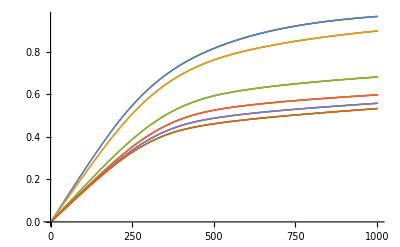

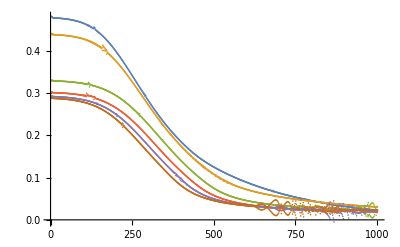

```mathematica
ListPlot[Table[MuDataShape[[i]],{i, 1, Length[TValues]}]]
ListPlot[Table[MuDotDataShape[[i]],{i, 1, Length[TValues]}]]
```

```mathematica
index = 1;
While[(index ≤Length[TValues]),
Export[StringJoin["~/Documents/MorphoCrypt/Mathematica/Solutions/amountsloughedshape_T_",ToString[TValues[[index]]],".csv"] ,Table[{tValues[[i]], MuDataShape[[index]][[i]]},{i, 1, Length[tValues]}]]; 
Export[StringJoin["~/Documents/MorphoCrypt/Mathematica/Solutions/sloughingrateshape_T_",ToString[TValues[[index]]],".csv"] ,Table[{tValues[[i]], MuDotDataShape[[index]][[i]]},{i, 1, Length[tValues]}]];
index=index+1];
```

```mathematica
(* For some reason it's easier to simulate ageing independently of the other quantities *)
```

```mathematica
AgeSolPreHomeostasisEulerian=NDSolve[{D[A[s, t],t]==1-(Evaluate[D[γ[s, t]/.SolPreHomeostasisEulerian,t]]/Evaluate[γ[s, t]/.SolPreHomeostasisEulerian])*A[s, t]+((1+n[s,t])*γ[s, t]/.SolPreHomeostasisEulerian)*D[(S0[s, t]/.SolPreHomeostasisEulerian),t]*D[A[s, t], s],
A[s, 0]==0}/.Subs,{A},{s,0,1},{t,0, 5},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

```mathematica
Manipulate[Plot[Evaluate[A[s, t]/.AgeSolPreHomeostasisEulerian], {s, 0, 1}],{t, 0, 5}]
```

```mathematica
AgeSolPreHomeostasisEulerian=NDSolve[{D[A[s, t],t]==1-(Evaluate[D[γ[s, t]/.SolPreHomeostasisEulerian,t]]/Evaluate[γ[s, t]/.SolPreHomeostasisEulerian])*A[s, t]+((1+n[s,t])*γ[s, t]/.SolPreHomeostasisEulerian)*D[(S0[s, t]/.SolPreHomeostasisEulerian),t]*D[A[s, t], s],
A[s, 0]==0}/.Subs,{A},{s,0,1},{t,0, 5},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

```mathematica
As=Function[s, Evaluate[A[s, t]/.AgeSolPreHomeostasisEulerian/.t-> 1]];
```

```mathematica
gValues = {0.25, 0.5, 1, 2, 4};
LeftBoundaryAgeDataScale={};
RightBoundaryAgeDataScale={};
index = 1;
```

```mathematica
While[(index ≤(Length[gValues])),  
g = gValues[[index]];
Clear[Gs];
(* Define functions needed for homeostasis *)
Gs=Function[s, g*gs[s]];

SolHomeostasisEulerian=NDSolve[{D[S0[s, t],s]==1/(αs[s]*γ[s,t]),
D[γ[s,t],t]==γ[s,t]*Gs[s]+αs[s]γ[s,t]D[γ[s,t],s]D[S0[s,t],t],
S0[s, 0]==S0s[s], S0[0,t]==0,γ[s,0]==gammas[s]}/.Subs,{S0,γ},{s,0,1},{t,0, 5},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];

AgeSolHomeostasisEulerian=NDSolve[{D[A[s, t],t]==1-gs[s]*A[s, t]+αs[s]*(γ[s, t]/.SolHomeostasisEulerian)*D[(S0[s, t]/.SolHomeostasisEulerian),t]*D[A[s, t], s],
A[s, 0]==As[s]}/.Subs,{A},{s,0,1},{t,0, 5},MaxStepSize->0.002,Method->{"IndexReduction"->Automatic}][[1]];

RightBoundaryAge=Function[t, A[s, t]/.AgeSolHomeostasisEulerian/.s-> 1];
LeftBoundaryAge=Function[t, A[s, t]/.AgeSolHomeostasisEulerian/.s-> 0];

AppendTo[LeftBoundaryAgeDataScale, LeftBoundaryAge[N[Range[0, 2500, 5]]/500]];
AppendTo[RightBoundaryAgeDataScale, RightBoundaryAge[N[Range[0, 2500, 5]]/500]];
index=index+1];
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

NDSolve::eerr: Warning: scaled local spatial error estimate of 288.271 at t = 5. in the direction of independent variable s is much greater than the prescribed error tolerance. Grid spacing with 401 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

5

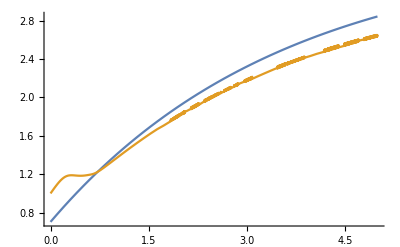

```mathematica
Plot[{LeftBoundaryAge[t], RightBoundaryAge[t]}, {t, 0, 5}]
```

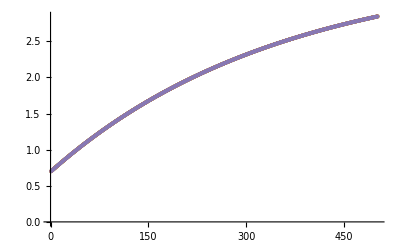

```mathematica
ListPlot[Table[LeftBoundaryAgeDataScale[[i]],{i, 1, Length[gValues]}]]
```

```mathematica
index = 1;
While[(index ≤Length[gValues]),
Export[StringJoin["~/Documents/MorphoCrypt/Mathematica/Solutions/leftboundaryagescale_g_",ToString[gValues[[index]]],".csv"] ,Table[{tValues[[i]], LeftBoundaryAgeDataScale[[index]][[i]]},{i, 1, Length[tValues]}]]; 
Export[StringJoin["~/Documents/MorphoCrypt/Mathematica/Solutions/rightboundaryagescale_g_",ToString[gValues[[index]]],".csv"] ,Table[{tValues[[i]], RightBoundaryAgeDataScale[[index]][[i]]},{i, 1, Length[tValues]}]];
index=index+1];
```

```mathematica
gValues
```

{0.25,0.5,1,2,4}

```mathematica
TValues = {0,1, 2, 3, 4,5};
LeftBoundaryAgeDataShape= {};
RightBoundaryAgeDataShape={};
```

```mathematica
index = 1;
While[(index ≤Length[TValues]),  
T = TValues[[index]];
Clear[Gs];
(* Define functions needed for homeostasis *)
Gs=Function[s, (Evaluate[D[γ[s, t]/.SolPreHomeostasisEulerian,t]]/.t-> T)/Evaluate[γ[s, t]/.SolPreHomeostasisEulerian/.t-> T]];
GsScale=NIntegrate[Gs[s], {s, 0, 1}];
GsScaled=Function[s,Evaluate[ (Gs[s] gsScale)/GsScale]];

SolHomeostasisEulerian=NDSolve[{D[S0[s, t],s]==1/(αs[s]*γ[s,t]),
D[γ[s,t],t]==γ[s,t]*(Gs[s]*gsScale)/GsScale+αs[s]γ[s,t]D[γ[s,t],s]D[S0[s,t],t],
S0[s, 0]==S0s[s], S0[0,t]==0,γ[s,0]==gammas[s]}/.Subs,{S0,γ},{s,0,1},{t,0, 5},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];


AgeSolHomeostasisEulerian=NDSolve[{D[A[s, t],t]==1-gs[s]*A[s, t]+αs[s]*(γ[s, t]/.SolHomeostasisEulerian)*D[(S0[s, t]/.SolHomeostasisEulerian),t]*D[A[s, t], s],
A[s, 0]==As[s]}/.Subs,{A},{s,0,1},{t,0, 5},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];

RightBoundaryAge=Function[t, A[s, t]/.AgeSolHomeostasisEulerian/.s-> 1];
LeftBoundaryAge=Function[t, A[s, t]/.AgeSolHomeostasisEulerian/.s-> 0];

AppendTo[LeftBoundaryAgeDataShape, LeftBoundaryAge[N[Range[0, 2500, 5]]/500]];
AppendTo[RightBoundaryAgeDataShape, RightBoundaryAge[N[Range[0, 2500, 5]]/500]];
index=index+1];
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

General::stop: Further output of NDSolve :: bcart will be suppressed during this calculation.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

General::stop: Further output of NDSolve :: ntdvdae will be suppressed during this calculation.

```mathematica
index = 1;
While[(index ≤Length[TValues]),
Export[StringJoin["~/Documents/MorphoCrypt/Mathematica/Solutions/leftboundaryageshape_T_",ToString[TValues[[index]]],".csv"] ,Table[{tValues[[i]], LeftBoundaryAgeDataShape[[index]][[i]]},{i, 1, Length[tValues]}]]; 
Export[StringJoin["~/Documents/MorphoCrypt/Mathematica/Solutions/rightboundaryageshape_T_",ToString[TValues[[index]]],".csv"] ,Table[{tValues[[i]], RightBoundaryAgeDataShape[[index]][[i]]},{i, 1, Length[tValues]}]];
index=index+1];
```

## Measuring velocities in homeostasis

```mathematica
sValues=N[Range[0, 500, 1]]/500;
S0Values=N[Range[0, 500, 1]]/500;
tValues = N[Range[0, 2500, 5]]/500;
```

```mathematica
LmuInterpolated=Interpolation[Table[{tValues[[i]], LmuControl[tValues[[i]]]},{i, 1, Length[tValues]}]];
αsInterpolated=Interpolation[Table[{sValues[[i]], αs[sValues[[i]]]},{i, 1, Length[sValues]}]];
gsInterpolated=Interpolation[Table[{sValues[[i]], gs[sValues[[i]]]},{i, 1, Length[sValues]}]];
sS0Interpolated=Interpolation[Table[{S0Values[[i]], sS0[S0Values[[i]]]},{i, 1, Length[S0Values]}]];
gammaS0Interpolated=Interpolation[Table[{S0Values[[i]], gammaS0[S0Values[[i]]]},{i, 1, Length[S0Values]}]];
pS0Interpolated=Interpolation[Table[{S0Values[[i]], pS0[S0Values[[i]]]},{i, 1, Length[S0Values]}]];
```

```mathematica
Lmu=Function[t, Evaluate[LmuInterpolated[t]]];
αs=Function[s, Evaluate[αsInterpolated[s]]];
gs=Function[s, Evaluate[gsInterpolated[s]]];
sS0=Function[S0,Evaluate[sS0Interpolated[S0]]];
gammaS0=Function[S0, Evaluate[gammaS0Interpolated[S0]]];
pS0=Function[S0, Evaluate[pS0Interpolated[S0]]];
```

```mathematica
(* Homeostasis in Lagrangian formulation TODO: Re-define Lmu so that it doesn't see that we're using the solution at t = 1*)
SolHomeostasisLagrangian=NDSolve[{D[s[S0],S0]==αs[s[S0]]*gammaS0[S0],
s[0]==0}/.Subs,{s},{S0,0,1},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];
```

InterpolatingFunction::dmval: Input value {1.00008} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
s[S0]/.SolHomeostasisLagrangian/.S0-> 1
```

1.00008

We’re going to have to do this in a bit of a hacky fashion, given the time-dependence of Lmu and the s-dependence of the incremental growth and stress profiles.

```mathematica
(* Initialise *)
t=0;
dt = 0.01;
sOld = sS0;
γOld=gammaS0;
pOld=pS0;
```

```mathematica
αs[0]-1
```

-0.571743

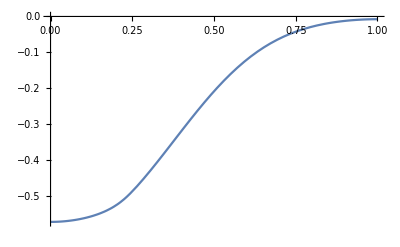

```mathematica
Plot[αs[s]-1,{s, 0, 1}]
```

```mathematica
gs[0]
```

0.283115

```mathematica
γOld[0]*(1+dt*gs[sOld[0]])
```

General::ivar: 0 is not a valid variable.

General::ivar: 1 is not a valid variable.

2.40403 (1+0.01 ∂_1 1.)

```mathematica
γNew=FunctionInterpolation[γOld[S0]*(1+dt*gs[sOld[S0]]),{S0, 0, 1}]
```

InterpolatingFunction[{{0., 1.}}, <>]

```mathematica
t = t+dt;
```

```mathematica
SolLagrange=NDSolve[{D[s[S0],S0]==(1+n[S0])*γNew[S0],
D[n[S0],S0]==k*(1+n[S0])*γNew[S0]*(s[S0]-pOld[S0]),
s[0]==0,n[0]==αs[0]-1}/.Subs,{s},{S0,0,Lmu[t]},Method-> "StiffnessSwitching",MaxStepSize-> 0.005][[1]];
```

NDSolve::ndsz: At S0 == 0.154342, step size is effectively zero; singularity or stiff system suspected.

```mathematica
pOld
```

InterpolatingFunction[{{0., 1.}}, <>]

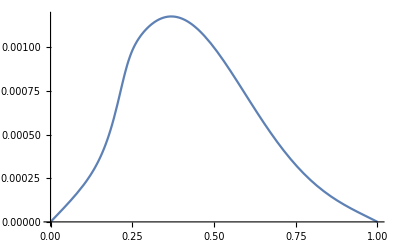

```mathematica
Plot[{sOld[S0]-pOld[S0]},{S0, 0, 1}]
```

```mathematica
Lmu[t]*(1+n[S0])*γNew[0]
```

2.41083 (-0.01 (0.-100. (LmuControl[0.]-LmuControl[0.01]))+LmuControl[0.01]) (1+n[S0])

```mathematica
(* Iterate over timesteps *) 
While[(t < 5.0),  
γNew=FunctionInterpolation[γOld[S0]*(1+dt*gs[sOld[S0]]),{S0, 0, 1}];
t = t+dt;
SolLagrange=NDSolve[{D[s[S0],S0]==Lmu[t]*(1+n[S0])*γNew[S0],
D[n[S0],S0]==Lmu[t]*k*(1+n[S0])*γNew[S0]*(s[S0]-pOld[S0]),
s[0]==1,s[1]==1}/.Subs,{s},{S0,0,1},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];
pNew=FunctionInterpolation[(η*dt*sOld[S0]+(1-η*dt)*pOld[S0])/.Subs,{S0, 0, 1}];
sNew=FunctionInterpolation[s[S0]/.SolLagrange,{S0, 0, 1}];
VNew=FunctionInterpolation[(sNew[S0]-sOld[S0])/dt,{S0, 0, 1}];
sOld =sOld;
γOld=γNew;
pOld=pNew;
];
```

NDSolve::ndsz: At S0 == 0.0345928, step size is effectively zero; singularity or stiff system suspected.

FunctionInterpolation::nreal: Near {S0} = {0.1}, the function did not evaluate to a real number.

FunctionInterpolation::nreal: Near {S0} = {0.2}, the function did not evaluate to a real number.

FunctionInterpolation::nreal: Near {S0} = {0.3}, the function did not evaluate to a real number.

General::stop: Further output of FunctionInterpolation :: nreal will be suppressed during this calculation.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[s[0] == 1s[1] == 1 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at S0 == 0..

General::stop: Further output of NDSolve :: ndnum will be suppressed during this calculation.

$Aborted

```mathematica
Lmu[t]
```

0.101222

## Effect of spatial heterogeneity of g(s)

```mathematica
WntScale=NIntegrate[W[s], {s, 0, 1}];
```

```mathematica
IncGammaWntPlotSets = {};
IncGammaWntSets = {};
LMuWntPlotSets = {};
LMuWntSets = {};
LMuWntData = {};
```

```mathematica
gValues
```

{0.25,0.5,1,2,4}

```mathematica
index = 1;
While[(index ≤Length[gValues]),  
SolHomeostasisEulerian=NDSolve[{D[S0[s, t],s]==1/(αs[s]*γ[s,t]),
D[γ[s,t],t]==γ[s,t]*((W[s]*NetIncGammaSets[[index]])/WntScale)+αs[s]γ[s,t]D[γ[s,t],s]D[S0[s,t],t],
S0[s, 0]==S0s[s], S0[0,t]==0,γ[s,0]==gammas[s]}/.Subs,{S0,γ},{s,0,1},{t,0, 5},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];

(* Calculate Lmu as a function of time *)
Lmu=Function[t, S0[s, t]/.SolHomeostasisEulerian/.s-> 1];

P1=Plot[(W[s]*NetIncGammaSets[[index]])/WntScale,{s, 0, 1}, PlotRange->Full,PlotStyle->ColorData[97,index+1]];
P2=Plot[Lmu[t],{t, 0, 5},PlotStyle->ColorData[97,index+1],PlotPoints-> 500];
AppendTo[IncGammaWntPlotSets,P1];
AppendTo[LMuWntPlotSets,P2];

AppendTo[IncGammaWntSets, (W[s]*NetIncGammaSets[[index]])/WntScale];
AppendTo[LMuWntSets, Lmu];

(*AppendTo[NetIncGammaSets, NIntegrate[gs[s], {s, 0, 1}]]*);
AppendTo[LMuWntData, Lmu[N[Range[0, 2500, 5]/500]]];
index=index+1];
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

General::stop: Further output of NDSolve :: ntdvdae will be suppressed during this calculation.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

General::stop: Further output of NDSolve :: bcart will be suppressed during this calculation.

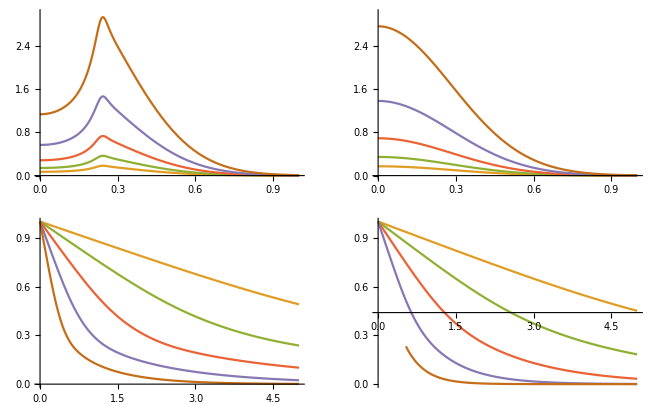

```mathematica
GraphicsGrid[{{Show[IncGammaPlotSets,PlotRange-> {{0, 1}, {0, 3}}],Show[IncGammaWntPlotSets,PlotRange-> {{0, 1}, {0, 3}}]},{Show[LMuPlotSets,PlotRange-> {{0, 5}, {0, 1}}],Show[LMuWntPlotSets,PlotRange-> {{0, 5}, {0, 1}}]}}]
```

Therefore both the amplitude and spatial heterogeneity of g(s) affects L_mu.

## Injuring the model

Injury means perturbations to both gamma and stress, i.e. a loss of material should release the built-up stress in the model.

```mathematica
ss=0.75;
```

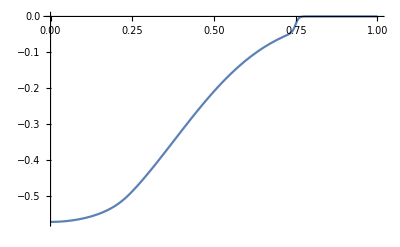

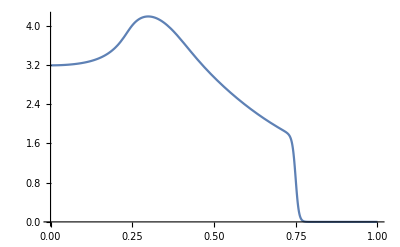

```mathematica
Plot[ns[s]*1/2(1+Tanh[100(ss-s)]),{s, 0, 1}]
Plot[gammaIC[s]*1/2(1+Tanh[100(ss-s)]),{s, 0, 1}]
```

```mathematica
Manipulate[Plot[γ[s, t]/.SolHomeostasisEulerianControl,{s, 0, 1}],{t, 0, 5}]
```

```mathematica
sValues=N[Range[0, 500, 1]]/500;
```

```mathematica
gammaICInterpolated = Interpolation[Table[{sValues[[i]], γ[sValues[[i]], t]/.SolHomeostasisEulerianControl/.t-> 1},{i, 1, Length[sValues]}]];
```

```mathematica
gammaIC = Function[s, gammaICInterpolated[s]];
```

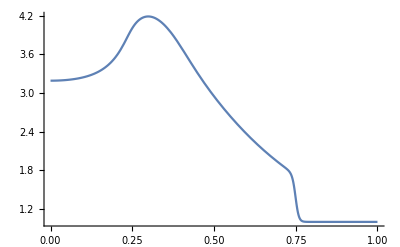

```mathematica
Plot[gammaIC[s]*1/2(1+Tanh[100(ss-s)]) + 1/2(1+Tanh[100(s-ss)]) ,{s,0, 1}]
```

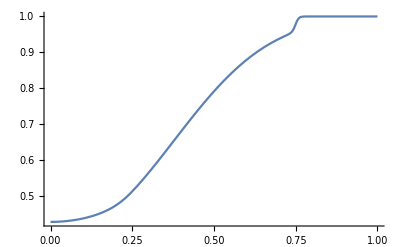

```mathematica
Plot[(1+ns[s]*1/2(1+Tanh[100(ss-s)])),{s, 0, 1}]
```

```mathematica
SolInjuredEulerian=NDSolve[{D[S0[s, t],s]==1/((1+ns[s]*1/2(1+Tanh[100(ss-s)]))*γ[s,t]),
D[γ[s,t],t]==γ[s,t]*(W[s]+μ*(ns[s]*1/2(1+Tanh[100(ss-s)])-ns)*1/2(1+Tanh[50(ns-ns[s]*1/2(1+Tanh[100(ss-s)]))]))+(1+ns[s]*1/2(1+Tanh[100(ss-s)]))*γ[s,t]*D[γ[s,t],s]*D[S0[s,t],t],
S0[s, 0]==S0s[s], S0[0,t]==0,γ[s,0]==gammaIC[s]*1/2(1+Tanh[100(ss-s)])+ 1/2(1+Tanh[100(s-ss)])}/.Subs,{S0,γ},{s,0,1},{t,0, 5},MaxStepSize->0.001,Method->{"IndexReduction"->Automatic}][[1]];
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::ndcf: Repeated convergence test failure at t == 0.; unable to continue.

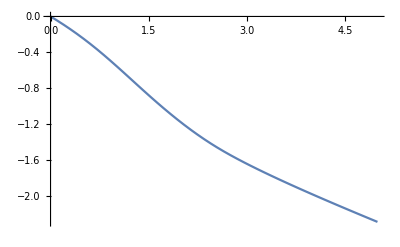

```mathematica
Plot[Log[LmuControl[t]], {t, 0, 5}]
```

```mathematica
LmuInjured=Function[t, Evaluate[S0[s,, t]/.SolInjuredEulerian/.s-> 1]];
```

```mathematica
Plot[LmuCheck[t], {t, 0, 5}]
```

-Graphics-

## Sensitivity of L_μ to initial perturbations.

Let’s use the profile at t = 1

```mathematica
αs = Function[s, 1+n[s, t]/.SolPreHomeostasisEulerian/.t-> 1];
gammas=Function[s,γ[s, t]/.SolPreHomeostasisEulerian/.t-> 1];S0s=Function[s,  S0[s, t]/.SolPreHomeostasisEulerian/.t-> 1];
gs=Function[s, (Evaluate[D[γ[s, t]/.SolPreHomeostasisEulerian,t]]/.t-> 1)/ Evaluate[γ[s, t]/.SolPreHomeostasisEulerian/.t-> 1]];
```

First, we need a control for L_μ.

```mathematica
SolHomeostasisEulerianControl=NDSolve[{D[S0[s, t],s]==1/(αs[s]*γ[s,t]),
D[γ[s,t],t]==γ[s,t]*gs[s]+αs[s]γ[s,t]D[γ[s,t],s]D[S0[s,t],t],
S0[s, 0]==S0s[s], S0[0,t]==0,γ[s,0]==gammas[s]}/.Subs,{S0,γ},{s,0,1},{t,0, 10},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

```mathematica
LmuControl=Function[t, S0[s, t]/.SolHomeostasisEulerianControl/.s-> 1];
```

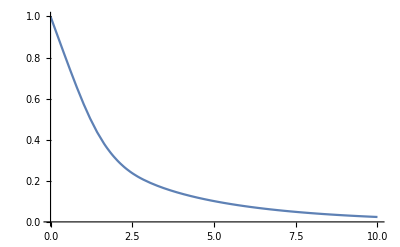

```mathematica
Plot[LmuControl[t], {t, 0, 10},PlotRange-> {{0,10}, {0, 1}}]
```

```mathematica
gValues = {0.125, 0.25, 0.5, 1, 1.1, 1.2};
```

```mathematica
IncGammaICShapePlotSets = {};
IncGammaICShapeSets = {};
LMuICShapePlotSets = {};
LMuICShapeSets = {};
LMuICShapeData = {};
ICShapeData={};
```

```mathematica
gValues
```

{0.125,0.25,0.5,1,1.1,1.2}

```mathematica
index = 6;
While[(index ≤6),  
SolHomeostasisEulerian=NDSolve[{D[S0[s, t],s]==1/(αs[s]*γ[s,t]),
D[γ[s,t],t]==γ[s,t]*(gs[s])+αs[s]γ[s,t]D[γ[s,t],s]D[S0[s,t],t],
S0[s, 0]==S0s[s], S0[0,t]==0,γ[s,0]==gValues[[index]]*gammas[s]}/.Subs,{S0,γ},{s,0,1},{t,0, 10},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];

(* Calculate Lmu as a function of time *)
Lmu=Function[t, S0[s, t]/.SolHomeostasisEulerian/.s-> 1];

P1=Plot[gValues[[index]]*gammas[s],{s, 0, 1}, PlotRange->Full,PlotStyle->ColorData[97,index+1]];
P2=Plot[Lmu[t],{t, 0, 10},PlotStyle->ColorData[97,index+1],PlotPoints-> 500];
AppendTo[IncGammaICShapePlotSets,P1];
AppendTo[LMuICShapePlotSets,P2];

AppendTo[IncGammaICShapeSets, gValues[[index]]*gammas[s]];
AppendTo[LMuICShapeSets, Lmu];

(*AppendTo[NetIncGammaSets, NIntegrate[gs[s], {s, 0, 1}]]*);
AppendTo[LMuICShapeData, Lmu[N[Range[0, 5000, 5]/500]]];
AppendTo[ICShapeData, gValues[[index]]*gammas[N[Range[0, 500, 5]/500]]];
index=index+1];
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[S0[1, 0] == 0.9999999999999999`S0[0, t] == 0γ[1, 0] == 1.0019323188344185` {0.125`, 0.25`, 0.5`, 1, 1.1`} ⟦ 6 ⟧ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

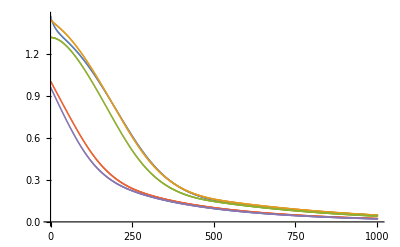

```mathematica
ListPlot[Table[LMuICShapeData[[i]],{i, 1,5}]]
```

```mathematica
(* Save the data *)
```

```mathematica
sValues=N[Range[0, 500, 5]]/500;
tValues=N[Range[0, 5000, 5]]/500;
```

```mathematica
index = 1;
While[(index ≤Length[gValues] - 1),
Export[StringJoin["~/Documents/MorphoCrypt/Mathematica/homeostaticinitialgrowth_g_",ToString[gValues[[index]]],".csv"] ,Table[{sValues[[i]], ICShapeData[[index]][[i]]},{i, 1, Length[sValues]}]]; 
Export[StringJoin["~/Documents/MorphoCrypt/Mathematica/sloughingboundaryinitialgrowth_g_",ToString[gValues[[index]]],".csv"] ,Table[{tValues[[i]], LMuICShapeData[[index]][[i]]},{i, 1, Length[tValues]}]];
index=index+1];
```

```mathematica
(* Perturb g(s) *)
δ=1;
SolHomeostasisEulerianPerturbed=NDSolve[{D[S0[s, t],s]==1/(αs[s]*γ[s,t]),
D[γ[s,t],t]==γ[s,t]*(gs[s]+δ*Exp[-(s-0.5)^2/.001])+αs[s]γ[s,t]D[γ[s,t],s]D[S0[s,t],t],
S0[s, 0]==S0s[s], S0[0,t]==0,γ[s,0]==gammas[s]}/.Subs,{S0,γ},{s,0,1},{t,0, 5},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

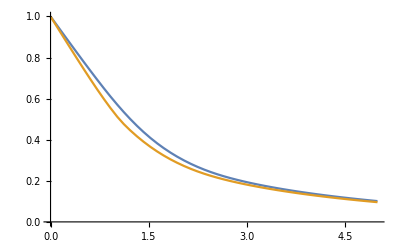

```mathematica
LmuPerturbed = Function[t, S0[s, t]/.SolHomeostasisEulerianPerturbed/.s-> 1];
Plot[{LmuControl[t], LmuPerturbed[t]}, {t, 0, 5},PlotRange-> {{0, 5}, {0,1 }}]
```

```mathematica
(* Perturb g(s) in the base but at later time. *)
δ=1;
SolHomeostasisEulerianDelayPerturbed=NDSolve[{D[S0[s, t],s]==1/(αs[s]*γ[s,t]),
D[γ[s,t],t]==γ[s,t]*(gs[s]+δ*Exp[-(s)^2/.001]*1/2*(1+Tanh[10*(t-2.5)]))+αs[s]γ[s,t]D[γ[s,t],s]D[S0[s,t],t],
S0[s, 0]==S0s[s], S0[0,t]==0,γ[s,0]==gammas[s]}/.Subs,{S0,γ},{s,0,1},{t,0, 5},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

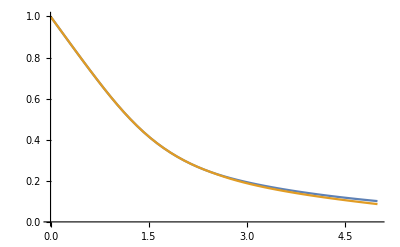

```mathematica
LmuDelayPerturbed = Function[t, S0[s, t]/.SolHomeostasisEulerianDelayPerturbed/.s-> 1];
Plot[{LmuControl[t], LmuDelayPerturbed[t]}, {t, 0, 5},PlotRange-> {{0, 5}, {0,1 }}]
```

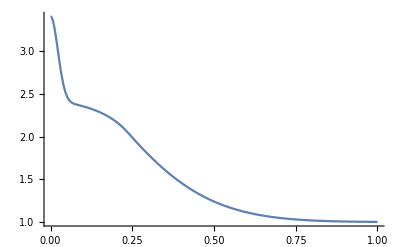

```mathematica
Plot[gammas[s]+δ*Exp[-(s-0)^2/.001], {s, 0, 1}]
```

```mathematica
(* Perturb g(s) in the base but at later time. *)
δ=-0.5;
SolHomeostasisEulerianICPerturbed=NDSolve[{D[S0[s, t],s]==1/(αs[s]*γ[s,t]),
D[γ[s,t],t]==γ[s,t]*gs[s]+αs[s]γ[s,t]D[γ[s,t],s]D[S0[s,t],t],
S0[s, 0]==S0s[s], S0[0,t]==0,γ[s,0]==gammas[s]+δ*Exp[-(s-0.5)^2/.001]}/.Subs,{S0,γ},{s,0,1},{t,0, 10},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

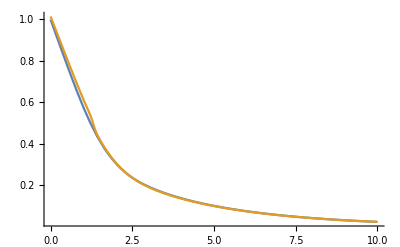

```mathematica
LmuICPerturbed = Function[t, S0[s, t]/.SolHomeostasisEulerianICPerturbed/.s-> 1];
Plot[{LmuControl[t], LmuICPerturbed[t]}, {t, 0, 10},PlotRange-> Full]
```

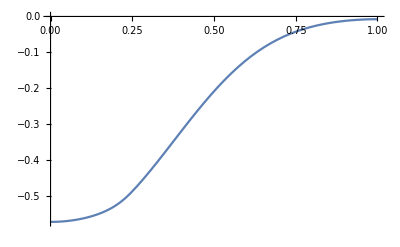

```mathematica
Plot[αs[s]-1, {s, 0, 1}]
```

```mathematica
(* Functions needed for Lagrangian formulation *)
```

```mathematica
γS0 = Function[S0, γ[S0, t]/.SolPreHomeostasisLagrangian/.t-> 1];
sS0=Function[S0, s[S0, t]/.SolPreHomeostasisLagrangian/.t-> 1];
nS0=Function[S0, n[S0, t]/.SolPreHomeostasisLagrangian/.t-> 1];
pS0=Function[S0, p[S0, t]/.SolPreHomeostasisLagrangian/.t-> 1];
```

```mathematica
γS0= γ[S0, t]/.SolPreHomeostasisLagrangian/.t-> 1
```

InterpolatingFunction[{{0., 1.}, {0., 6.}}, <>][S0,1]

```mathematica
(* Lagrangian formulation for homeostasis *)
SolHomeostasisLagrangian=NDSolve[{D[s[S0, t],S0]==(1+n[S0, t])*γ[S0,t],
D[γ[S0,t],t]==γ[S0,t]*gs[s[S0, t]],
D[n[S0, t], S0]==k*(1+n[S0, t])*γ[S0,t]*(s[S0, t]-p[S0, t]),
D[p[S0, t], t]==ρ*(s[S0, t]-p[S0, t]),
s[0,t]==0,s[1,t]==1,γ[S0,0]==γS0[S0],s[S0,0]==sS0[S0], p[S0, 0]==pS0[S0], n[S0, 0]==nS0[S0]}/.Subs,{s,γ, n, p},{S0,0,1},{t,0,6},MaxStepSize-> 0.005,Method->{"IndexReduction"->Automatic}][[1]];
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::delpde: Delay partial differential equations are not currently supported by NDSolve.

```mathematica
Subs
```

{μ→10,ρ→10,ns→-0.5,k→1000}

```mathematica
NIntegrate[gs[s], {s, 0, 1}]
```

0.244066

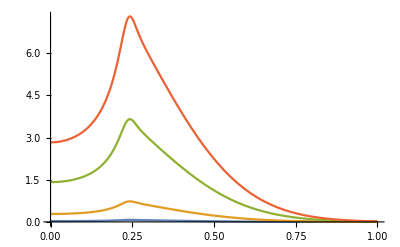

```mathematica
Plot[{0.1*gs[s],  gs[s], 5*gs[s], 10*gs[s]}, {s, 0, 1},PlotRange-> Full]
```

```mathematica
Plot[{W[s]+μ*(αs[s]-1-ns)*1/2*(1+Tanh[50*(ns-αs[s]+1)])/.Subs,gs[s]},{s, 0, 1}]
```

-Graphics-

$Aborted

```mathematica
SolHomeostasisEulerianControl=NDSolve[{D[S0[s, t],s]==1/((1+ns[s])*γ[s,t]),
D[γ[s,t],t]==γ[s,t]*gs[s]+αs[s]γ[s,t]D[γ[s,t],s]D[S0[s,t],t],
S0[s, 0]==S0s[s], S0[0,t]==0,γ[s,0]==gammas[s]}/.Subs,{S0,γ},{s,0,1},{t,0, 5},MaxStepSize->0.005,Method->{"IndexReduction"->Automatic}][[1]];
```

## Homeostasis consistency

```mathematica
(* Define the coupled ODE system *)
```

```mathematica
StressHomeostasisEulerianOde[R:{__?NumericQ}]:=Block[{sol, s, n, u, v,cond},sol=NDSolve[{D[n[s],s]==u[s],D[u[s],s]==k+(ρ*u[s])/v[s],D[v[s],s]==(u[s]*v[s])/(1+n[s])-(W[s]+μ*(n[s]-ns)*1/2*(1+Tanh[50*(ns-n[s])])),n[0.001]==R[[1]],u[0.001]==(0.001*k*(W[0]+μ*(R[[1]]-ns)*1/2*(1+Tanh[50*(ns-R[[1]])])))/(ρ+(W[0]+μ*(R[[1]]-ns)*1/2*(1+Tanh[50*(ns-R[[1]])]))),v[0.001]==-0.001*(W[0]+μ*(R[[1]]-ns)*1/2*(1+Tanh[50*(ns-R[[1]])]))},{n[s],u[s],v[s]},{s, 0.001, 1},Method-> "StiffnessSwitching"][[1]];
cond={u[s]}/.sol/.s-> 1
];
EquilStressSolHomeostasisEulerian[R_]:=NDSolve[{D[n[s],s]==u[s],D[u[s],s]==k+(ρ*u[s])/v[s],D[v[s],s]==(u[s]*v[s])/(1+n[s])-(W[s]+μ*(n[s]-ns)*1/2*(1+Tanh[50*(ns-n[s])])),n[0.001]==R[[1]],u[0.001]==(0.001*k*(W[0]+μ*(R[[1]]-ns)*1/2*(1+Tanh[50*(ns-R[[1]])])))/(ρ+(W[0]+μ*(R[[1]]-ns)*1/2*(1+Tanh[50*(ns-R[[1]])]))),v[0.001]==-0.001*(W[0]+μ*(R[[1]]-ns)*1/2*(1+Tanh[50*(ns-R[[1]])]))},{n,u,v},{s, 0.001, 1},Method-> "StiffnessSwitching"][[1]];
```

```mathematica
D[W[s],{s, 2}]/.s-> 0
```

-78.125

```mathematica
1/0.16^2
```

39.0625

```mathematica
W[s]
```

ⅇ^(-6.25 s^2)

```mathematica
Krho[ρ_]:=-(D[W[s],{s, 2}]/.s-> 0)/μ*(ρ/(W[0]+μ*(R0[[1]]-ns))+1);
```

```mathematica
D[W[s],{s, 2}]
```

W''[s]

```mathematica
Krho[0]
```

7.8125

```mathematica
μ=10;
ns=-0.5;
R0={-0.55};
```

```mathematica
(D[Exp[-s^2/σ^2],{s, 2}])/μ/.s-> 0
```

-2/(μ σ^2)

```mathematica
Krho[ρ]
```

164.063

```mathematica
FindMaximum[W[s]+μ*(n[s]-ns)*1/2*(1+Tanh[50*(ns-n[s])])/.sol,{s,0.05}]
```

InterpolatingFunction::dmval: Input value {-0.45} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{0.503323,{s→-5.36099×10^-8}}

```mathematica
Clear[ρ]
Solve[Krho[ρ]==k,ρ]
```

{{ρ→0.064 (-7.8125+1. k)}}

```mathematica
K = 1000;
```

```mathematica
FindRoot[StressHomeostasisEulerianOde[R],{R, R0}]
```

NDSolve::ndsz: At s == 0.00687304, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At s == 0.175387, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At s == 0.22516, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{R→{-0.587096}}

```mathematica
StressHomeostasisEulerianOde[{-0.5870964508031626}]
```

{2.03384×10^-9}

```mathematica
u[s]/.sol/.s-> 1
```

2.03384×10^-9

```mathematica
μ = 10;
ns = -0.5;
ρ=10;
k = 1000;
```

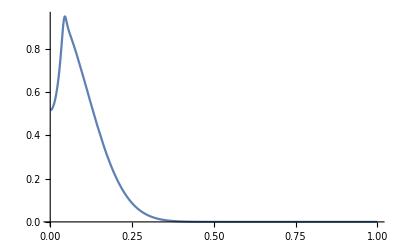

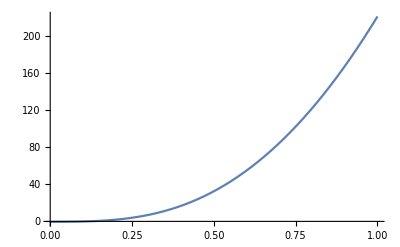

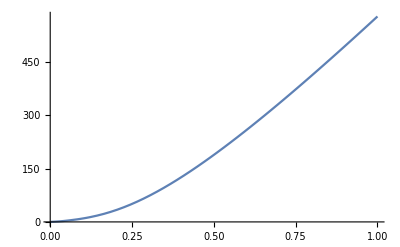

```mathematica
sol=EquilStressSolHomeostasisEulerian[{-0.5487254669513919}];
Plot[W[s]+μ*(n[s]-ns)*1/2*(1+Tanh[50*(ns-n[s])])/.sol,{s, 0.001, 1},PlotRange-> All]
Plot[{n[s]/.sol},{s, 0.001, 1},PlotRange-> All]
Plot[{u[s]/.sol},{s, 0.001, 1},PlotRange-> All]
```

```mathematica
nhom=Function[s, n[s]/.sol];
phom=Function[s, s-(u[s]/.sol)/k];
vhom=Function[s, v[s]/.sol];
ghom=Function[s,W[s]+μ*(n[s]-ns)*1/2*(1+Tanh[50*(ns-n[s])])/.sol];
```

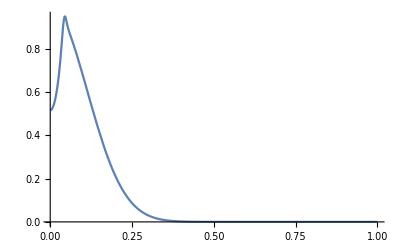

```mathematica
Plot[ghom[s],{s, 0.001, 1}]
```

```mathematica
gammaHomeostasisSol =NDSolve[{D[γ[s,t],t]==γ[s,t]*ghom[s]+vhom[s]*D[γ[s,t],s],
γ[s,0]==0.27929608549211804}/.Subs,{γ},{s,0.01,1},{t,0, 5},MaxStepSize-> 0.005][[1]];
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

```mathematica
Manipulate[Plot[γ[s,t]/.gammaHomeostasisSol/.t-> T,{s, 0.01, 1}],{T, 0, 5}]
```

ReplaceAll::reps: {gammaHomeostasisSol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
S0HomeostasisSol =NDSolve[{D[S0[s,t],s]==1/((1+nhom[s])*γ[s,t]/.gammaHomeostasisSol),
S0[0.01,t]==0.01}/.Subs,{S0},{s,0.01,1},{t,0, 5}][[1]];
```

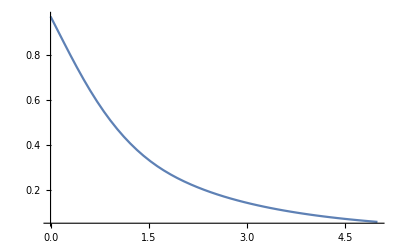

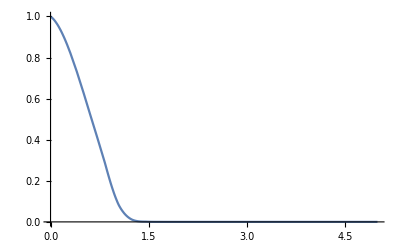

```mathematica
Lmu=Function[t,S0[s,t]/.S0HomeostasisSol/.s-> 1];
Plot[Lmu[t],{t, 0, 5},PlotRange-> All]
```

```mathematica
D[Exp[-s^2/σ^2],{s, 2}]
```

(4 ⅇ^(-s^2/σ^2) s^2)/σ^4-(2 ⅇ^(-s^2/σ^2))/σ^2

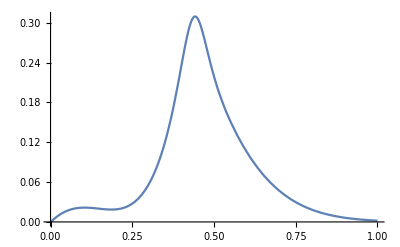

```mathematica
Plot[W[s]+10*(n[s]-ns)*1/2*(1+Tanh[50*(ns-n[s])])/.Sol,{s, 0, 1},PlotRange-> All]
```